```mathematica
ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]];

<<NLSMAlgebra`;   (*Loads the math logic*)
<<NLSMLisp`;     (*Loads the translator& Lisp engine*)
<<NLSMVisuals`;
```

Full Multi-Term Report saved to: report/S2p_a.pdf

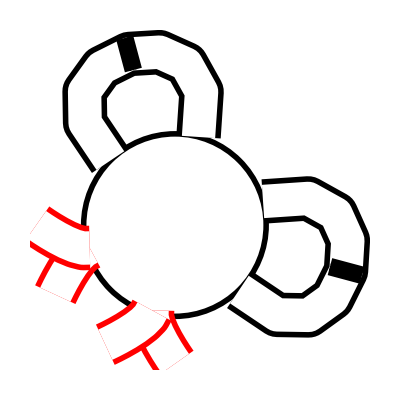
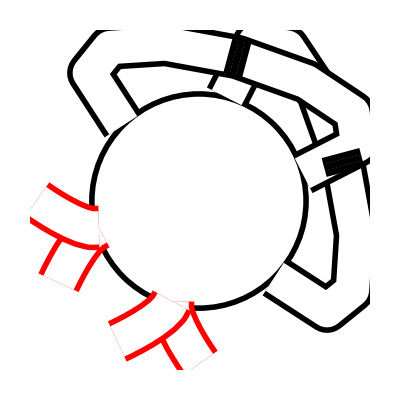
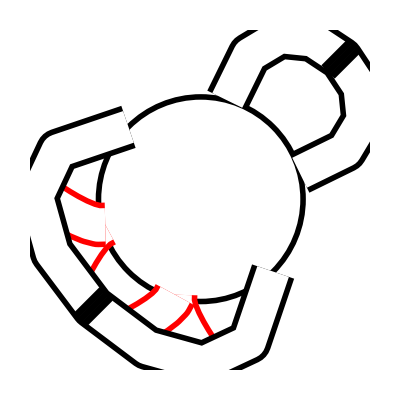
Term 1
Tr[Φ(R).σ_3.W(R).W(R).Φ(R).σ_3.W(R).W(R)] |  | 
ID | Diagram | Value
1 | -Graphics- | 0
2 | -Graphics- | -1/8 t Ð[0]^2 Tr[Perp[Φ[R]].Perp[Φ[R]]]
3 | -Graphics- | 0
____________________

```mathematica
SetDirectory[NotebookDirectory[]];
pathReport="report/S2p_a.pdf";

factor=1/(2 t);
data=EvaluateModel[ToLispString[Tr[Φ[r].Subscript[σ, 3].W[r].W[r].Φ[r].Subscript[σ, 3].W[r].W[r]]]];
saveReport[data,pathReport,factor];
generateReport[data,factor]
```

Full Multi-Term Report saved to: report/S2p_b.pdf

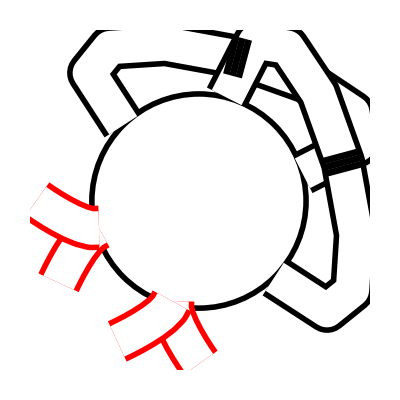
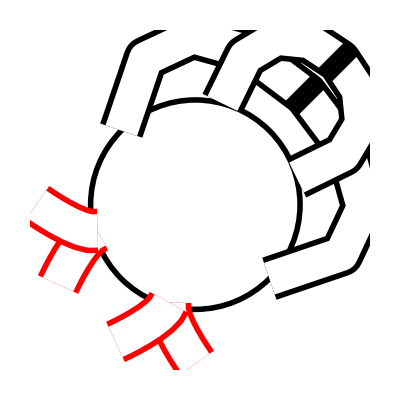
Term 1
Tr[Φ(R).σ_3.Φ(R).σ_3.W(R).W(R).W(R).W(R)] |  | 
ID | Diagram | Value
1 | -Graphics- | 0
2 | -Graphics- | 0
3 | -Graphics- | 0
____________________

```mathematica
SetDirectory[NotebookDirectory[]];
pathReport="report/S2p_b.pdf";

factor=λ/(2 t);
data=EvaluateModel[ToLispString[Tr[Φ[r].Subscript[σ, 3].Φ[r].Subscript[σ, 3].W[r].W[r].W[r].W[r]]]];
saveReport[data,pathReport,factor];
generateReport[data,factor]
```

```mathematica
SetDirectory[NotebookDirectory[]];
pathReport="report/S2p_c.pdf";

factor=(1+λ)/(2 t);
data=EvaluateModel[ToLispString[Tr[Φ[r].Subscript[σ, 3].W[r].Φ[r].Subscript[σ, 3].W[r].W[r].W[r]]]];
saveReport[data,pathReport,factor];
generateReport[data,factor]
```

Full Multi-Term Report saved to: report/S2p_c.pdf

Term 1
Tr[Φ(R).σ_3.W(R).Φ(R).σ_3.W(R).W(R).W(R)] |  | 
ID | Diagram | Value
1 | -Graphics- | 0
2 | -Graphics- | 0
3 | -Graphics- | 0
____________________

Full Multi-Term Report saved to: report/S1squared_11.pdf

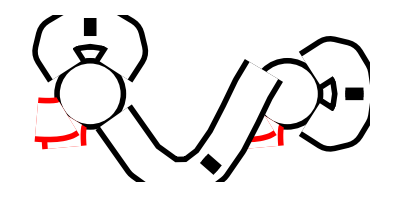
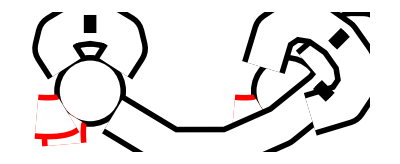
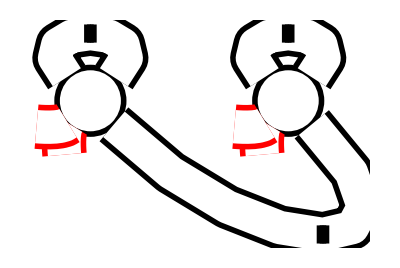
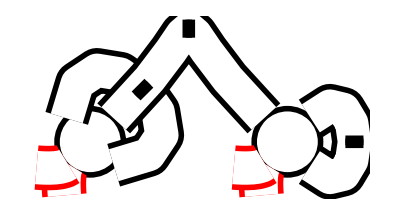
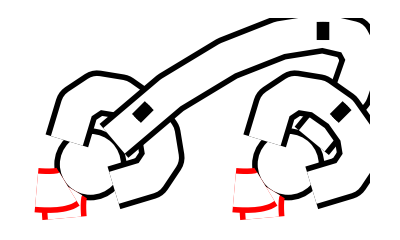
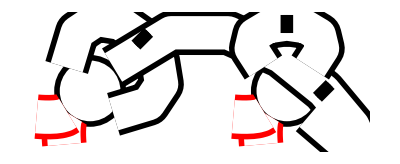
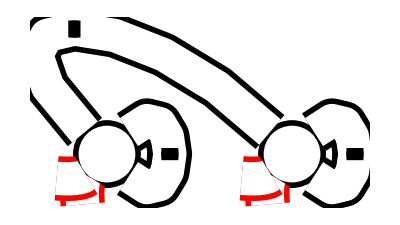
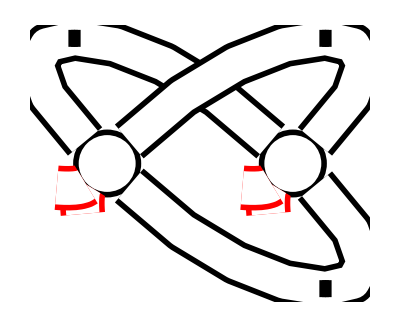
Term 1
Tr[Φ(X).∇_X .W(X).W(X).W(X)].Tr[Φ(Y).∇_Y .W(Y).W(Y).W(Y)] |  | 
ID | Diagram | Value
1 | -Graphics- | 0
2 | -Graphics- | 0
3 | -Graphics- | 0
4 | -Graphics- | 0
5 | -Graphics- | 0
6 | -Graphics- | 0
7 | -Graphics- | 0
8 | -Graphics- | 1/64 t (1+λ)^2 Tr[Perp[Φ[X]].Der[X].Der[Y].Π[X-Y].Π[X-Y].Π[X-Y].Perp[Φ[Y]]]
9 | -Graphics- | 0
10 | -Graphics- | 0
11 | -Graphics- | 0
12 | -Graphics- | 0
13 | -Graphics- | 0
14 | -Graphics- | 0
15 | -Graphics- | 0
____________________

```mathematica
SetDirectory[NotebookDirectory[]];
pathReport="report/S1squared_11.pdf";

factor=-(1+λ)^2/(8 t^2);
data=EvaluateModel[ToLispString[Tr[Φ[x].W[x,Der[x]].W[x].W[x]]Tr[Φ[y].W[y,Der[y]].W[y].W[y]]]];
saveReport[data,pathReport,factor];
generateReport[data,factor]
```

```mathematica
SetDirectory[NotebookDirectory[]];
pathReport="report/S1squared_13.pdf";

factor=-(1+λ)^2/(8 t^2);
data=EvaluateModel[ToLispString[Tr[Φ[x].W[x,Der[x]].W[x].W[x]]Tr[Φ[y].W[y].W[y].W[y,Der[y]]]]];
saveReport[data,pathReport,factor];
generateReport[data,factor]
```

Full Multi-Term Report saved to: report/S1squared_13.pdf

Term 1
Tr[Φ(X).∇_X .W(X).W(X).W(X)].Tr[Φ(Y).W(Y).W(Y).∇_Y .W(Y)] |  | 
ID | Diagram | Value
1 | -Graphics- | 0
2 | -Graphics- | 0
3 | -Graphics- | 0
4 | -Graphics- | 0
5 | -Graphics- | 0
6 | -Graphics- | 0
7 | -Graphics- | 0
8 | -Graphics- | 1/64 t (1+λ)^2 Tr[Perp[Φ[X]].Der[X].Π[X-Y].Π[X-Y].Der[Y].Π[X-Y].Perp[Φ[Y]]]
9 | -Graphics- | 0
10 | -Graphics- | 0
11 | -Graphics- | 0
12 | -Graphics- | 0
13 | -Graphics- | 0
14 | -Graphics- | 0
15 | -Graphics- | 0
____________________

```mathematica
SetDirectory[NotebookDirectory[]];
pathReport="report/S1squared_31.pdf";

factor=-(1+λ)^2/(8 t^2);
data=EvaluateModel[ToLispString[Tr[Φ[x].W[x].W[x].W[x,Der[x]]]Tr[Φ[y].W[y,Der[y]].W[y].W[y]]]];
saveReport[data,pathReport,factor];
generateReport[data,factor]
```

Full Multi-Term Report saved to: report/S1squared_31.pdf

Term 1
Tr[Φ(X).W(X).W(X).∇_X .W(X)].Tr[Φ(Y).∇_Y .W(Y).W(Y).W(Y)] |  | 
ID | Diagram | Value
1 | -Graphics- | 0
2 | -Graphics- | 0
3 | -Graphics- | 0
4 | -Graphics- | 0
5 | -Graphics- | 0
6 | -Graphics- | 0
7 | -Graphics- | 0
8 | -Graphics- | 1/64 t (1+λ)^2 Tr[Perp[Φ[X]].Der[Y].Π[X-Y].Π[X-Y].Der[X].Π[X-Y].Perp[Φ[Y]]]
9 | -Graphics- | 0
10 | -Graphics- | 0
11 | -Graphics- | 0
12 | -Graphics- | 0
13 | -Graphics- | 0
14 | -Graphics- | 0
15 | -Graphics- | 0
____________________

```mathematica
SetDirectory[NotebookDirectory[]];
pathReport="report/S1squared_33.pdf";

factor=-(1+λ)^2/(8 t^2);
data=EvaluateModel[ToLispString[Tr[Φ[x].W[x].W[x].W[x,Der[x]]]Tr[Φ[y].W[y].W[y].W[y,Der[y]]]]];
saveReport[data,pathReport,factor];
generateReport[data,factor]
```

Full Multi-Term Report saved to: report/S1squared_33.pdf

Term 1
Tr[Φ(X).W(X).W(X).∇_X .W(X)].Tr[Φ(Y).W(Y).W(Y).∇_Y .W(Y)] |  | 
ID | Diagram | Value
1 | -Graphics- | 0
2 | -Graphics- | 0
3 | -Graphics- | 0
4 | -Graphics- | 0
5 | -Graphics- | 0
6 | -Graphics- | 0
7 | -Graphics- | 0
8 | -Graphics- | 1/64 t (1+λ)^2 Tr[Perp[Φ[X]].Π[X-Y].Π[X-Y].Der[X].Der[Y].Π[X-Y].Perp[Φ[Y]]]
9 | -Graphics- | 0
10 | -Graphics- | 0
11 | -Graphics- | 0
12 | -Graphics- | 0
13 | -Graphics- | 0
14 | -Graphics- | 0
15 | -Graphics- | 0
____________________

Full Multi-Term Report saved to: report/S0pS2_13.pdf

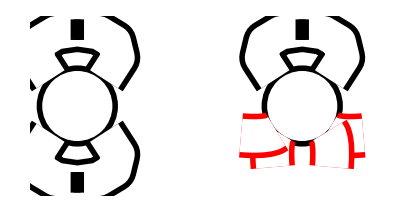
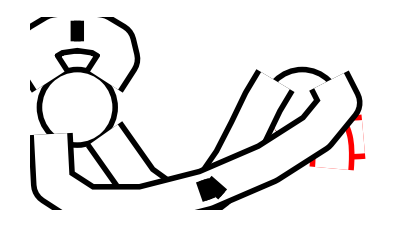
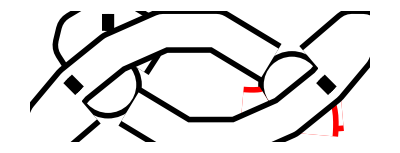
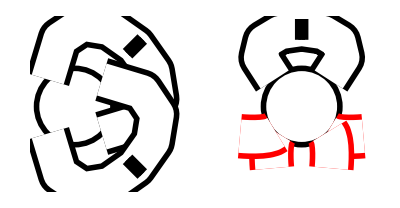
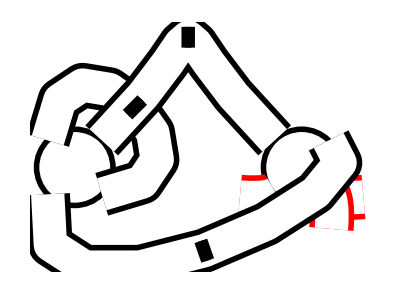
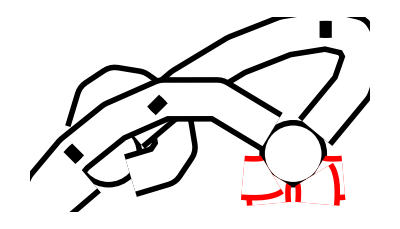
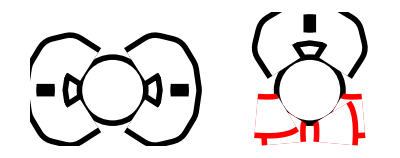
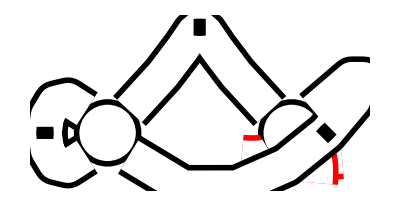
Term 1
Tr[∇_Y .W(Y).W(Y).∇_Y .W(Y).W(Y)].Tr[Φ(X).σ_3.Φ(X).σ_3.W(X).W(X)] |  | 
ID | Diagram | Value
1 | -Graphics- | 0
2 | -Graphics- | 0
3 | -Graphics- | 0
4 | -Graphics- | 0
5 | -Graphics- | 0
6 | -Graphics- | 0
7 | -Graphics- | 0
8 | -Graphics- | 0
9 | -Graphics- | 0
10 | -Graphics- | 0
11 | -Graphics- | 0
12 | -Graphics- | 0
13 | -Graphics- | 0
14 | -Graphics- | 0
15 | -Graphics- | 0
____________________

```mathematica
SetDirectory[NotebookDirectory[]];
pathReport="report/S0pS2_13.pdf";

factor=-(1+λ)^2/(8 t^2);
data=EvaluateModel[ToLispString[Tr[Φ[x].Subscript[σ, 3].Φ[x].Subscript[σ, 3].W[x].W[x]]Tr[W[y,Der[y]].W[y].W[y,Der[y]].W[y]]]];
saveReport[data,pathReport,factor];
generateReport[data,factor]
```

Full Multi-Term Report saved to: report/RG_1_TEST.pdf

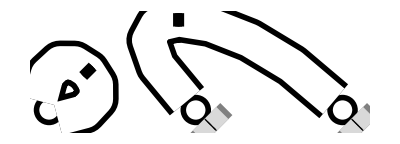
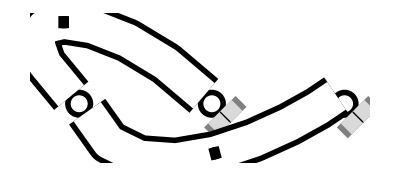
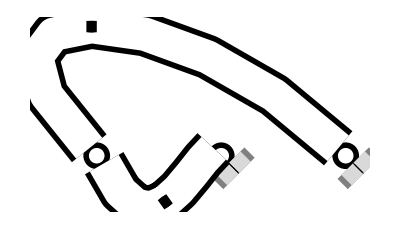
Term 1
Tr[Ε(X).∇_X .W(X).∇_X .W(X)].Tr[ϕ(Y).σ_3.W(Y)].Tr[ϕ(Z).σ_3.W(Z)] |  | 
ID | Diagram | Value
1 | -Graphics- | 0
2 | -Graphics- | -1/2 Dp π ν0 Tr[Para[Ε[X]].Der[X].Π[X-Y].Perp[ϕ[Y]].Der[X].Π[X-Z].Perp[ϕ[Z]]]
3 | -Graphics- | -1/2 Dp π ν0 Tr[Para[Ε[X]].Der[X].Π[X-Z].Perp[ϕ[Z]].Der[X].Π[X-Y].Perp[ϕ[Y]]]
____________________

```mathematica
SetDirectory[NotebookDirectory[]];
pathReport="report/RG_1_TEST.pdf";

factor=((-ⅈ π ν0 Dp)/4)((ⅈ (π ν0)^2)/2) ((-4/(π ν0))/t)^2;
data=EvaluateModel[ToLispString[Tr[Ε[x].W[x,Der[x]].W[x,Der[x]]]Tr[ϕ[y].Subscript[σ, 3].W[y]]Tr[ϕ[z].Subscript[σ, 3].W[z]]]];
saveReport[data,pathReport,factor];
generateReport[data,factor]
```